#### Lennard-Jones potential Or why perfume does not spread across your room in 0.02 seconds

Derivation and explanation of the concept
It is known that when molecules are infinitely apart, they do not interact with each other.

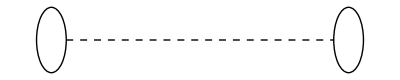

```mathematica
Graphics[{
Circle[{5,0},0.5],
Circle[{-5,0},0.5],
{Dashed,Line[{{-4.5,0},{4.5,0}}]}
}]
```

However, as the molecules approach closer to each other, they start interacting with each other:

```mathematica
Graphics[{
Circle[{2,0},0.25],
Circle[{-2,0},0.25],
{Dashed,Line[{{-1.75,0},{1.75,0}}]},
Arrow[{{-1.75,0},{-1,0}}],
Arrow[{{1.75,0},{1,0}}],
Arrowheads[{-0.04,0.04}],
	Arrow[{{-2,-1},{2,-1}}],
}]
```

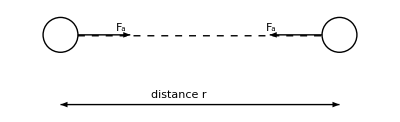

Where F_a is attractive force and r is distance between the molecules/atoms
When the molecules approach too close to each other, they start to repel each other - repulsive forces dominate:

```mathematica
Graphics[{
Circle[{0.25,0},0.25],
Circle[{-0.25,0},0.25],
Arrow[{{-0.5,0},{-1,0}}],
Arrow[{{0.5,0},{1,0}}]
}]
```

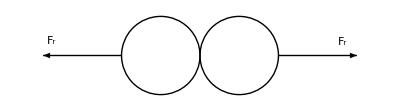

Where F_r is repulsive force between the molecules.

The natural question is how those two forces (attractive and repulsive) complement each other into one uniform system.

It turns out that attractive force can be best described by London dispersion forces: forces, which are induced by instantaneous electron density shift in atoms/molecules, which causes neutral atoms/molecules to have partially electronegative and electropositive side.

This attractive energy can be described as:

```mathematica
Subscript[U, a](r)=-3/2 Subscript[α, 1] Subscript[α, 2](Subscript[I, 1] Subscript[I, 2])/(Subscript[I, 1]+Subscript[I, 2])·1/r^6
```

The function can be simplified to:

```mathematica
Subscript[U, a](r)=-4ϵ(σ/r)^6
```

Here, ϵ is the potential energy, required to infinitely separate two atoms from equilibrium distance r_(0;)

```mathematica
σ=Subscript[r, 0]/2^(1/6)
```

The attractive force is negligible at great distance, but becomes increasingly more significant as the get closer.
Below is a typical shape of attractive energy potential with increasing distance (Helium atoms are used for the example calculation):

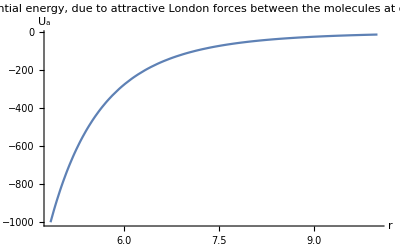

```mathematica
Plot[-4*11000*((258.*10^-12)/r)^6,{r,0,10^-9},
	AxesLabel->{Style["r",Medium,Black],
			     Style["U_a",Medium,Black]
			},
	PlotLabel->Style["Potential energy, due to attractive London 
forces between the molecules at distance r",
					FontSize->13,
					FontColor->Black
					],
	PlotRange->{0,-1000}
	]
```

On the other hand, the repulsive force is described by Pauli exclusion principle - no two electrons can occupy the same orbitals in an atom. As the two atoms get too close, their electrons start to share the orbitals and therefore this repulsive force becomes highly dominant. It is described by:

```mathematica
Subscript[U, r](r)=-4ϵ(σ/r)^12
```

Which increases rapidly, as the atoms approach to each other.
Below is the shape of the potential energy due to repulsive forces for He atoms:

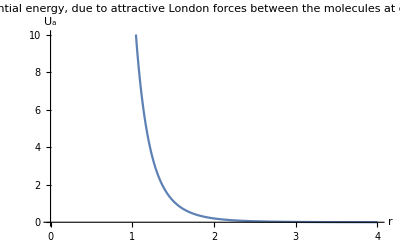

```mathematica
Plot[4*11000*((258.*10^-12)/r)^6,{r,0,4*10^-9},
	AxesLabel->{Style["r",Medium,Black],
			     Style["U_a",Medium,Black]
			},
	PlotLabel->Style["Potential energy, due to attractive London
 forces between the molecules at distance r",
					FontSize->13,
					FontColor->Black
					],
	PlotRange->{0,10}
	]
```

The total potential energy between the two molecules is:

```mathematica
Subscript[U, total](r)=-4ϵ[(σ/r)^12-(σ/r)^6]
```

Therefore, the total function of potential energy between the two atoms/molecules can be viewed:

```mathematica
σ={258.*10^-12,342.*10^-12,427.*10^-12,527.*10^-12,412.*10^-12,297.*10^-12,406.*10^-12}; (* sigma values of the substances *)
ϵ={11000,128000,536000,454000,368000,34000,236000}; (* epsilon values *)
textValues={"He","Ar","Br_2","C_6H_6","Cl_2","H_2","Xe"}; (* substances used *)
Manipulate[Plot[4 ϵ⟦type⟧*((σ⟦type⟧/r)^12-(σ⟦type⟧/r)^6),{r,0,10^-9}, (* creating a plot for Lennard Jones potential function, where σ⟦type⟧ and ϵ⟦type⟧ are the
parameters, varying with the "type" of substance: *look at the bottom of the code* type varies from 1 to the length of the length of σ list, 
and at the same time the "type" values from 1 to 7 are assigned to look in the form "substance, σ value, ϵ value" *)
	AxesLabel->{Style["r",Medium,Black],
			     Style["U_a",Medium,Black]
			},
	PlotLabel->Style["Overall potential energy between the molecules at distance r",
					FontSize->13,
					FontColor->Black
					],
	PlotRange->{Automatic,{ϵ⟦type⟧/5,-ϵ⟦type⟧-2000}}
	],
		{{type,1,"Substance:"},Thread[
					Range@Length@σ->Row/@(
					Riffle[#,", "]&/@
						Transpose[{textValues,"(σ)"σ,"(ϵ)"ϵ}]
)]}
]
```

The two particles will be at equilibrium at distance r_0, where the attractive force is the greatest. However, as the molecules get closer to each other, repulsive forces start dominating.
However, the scale of interaction between the different molecules is not clear unless drawn within the same graph:

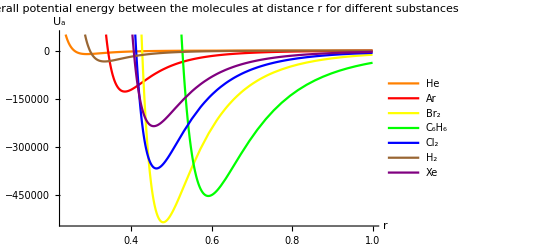

```mathematica
Plot[Evaluate@Table[ (* why evaluate changes everything here? *)
4 ϵ⟦type⟧*((σ⟦type⟧/r)^12-(σ⟦type⟧/r)^6),
{type,Length[σ]}],
{r,0,10^-9},
	PlotStyle->{Orange,Red,Yellow,Green,Blue,Brown,Purple},
	AxesLabel->{Style["r",Medium,Black],
			     Style["U_a",Medium,Black]
			},
	PlotLabel->Style["Overall potential energy between the molecules at distance r
	for different substances",
					FontSize->13,
					FontColor->Black
					],
	PlotRange->{Automatic,{50000,-540000}},
	PlotLegends->{textValues}
]
```

#### The visualisation of interaction between the particles

You can explore how two Helium particles interact with each other in the following simulation: one particle can be adjusted at a fixed point, while the other interacts with the first one accordingly.

```mathematica
pos={0,0};x={2*10^-10,0};v=0;a=0;m=4*1.66*10^-27;
Slider[Dynamic[pos⟦1⟧],{-5*10^-10,5*10^-10}]
Dynamic[
r=pos⟦1⟧-x⟦1⟧;
a=4 ϵ⟦1⟧ (-(12 σ⟦1⟧^12)/r^13+(6 σ⟦1⟧^6)/r^7)*m;
v+=0.5*a;
x⟦1⟧+=0.5*a;
Graphics[{
InfiniteLine[{{0,0},{1,0}}],
Disk[{pos⟦1⟧,0},1*10^-10],
Disk[{x⟦1⟧,0},1*10^-10]},
PlotRange->1*10^-9
]
]
```

In this way it is made sure that the particles attract each other, however, repulsive force prevents them from getting too close.

Mantas Pastolis
mantas.pastolis.16@ucl.ac.uk